```mathematica
(*Messing around with something LIKE a cellular automaton, where there's a repeating pattern of one or two-input binary logic gates for each step*)
```

```mathematica
alternateArray[array_]:=Table[If[EvenQ[i],Identity,Map[Not]][array[[i]]],{i,Length[array]}]
```

```mathematica
gACell[init_,stateI_,ruleI_,rule_]:=rule[[ruleI,2]]@@Table[init[[Mod[stateI+ruleI-1+rule[[ruleI,1,cellRuleI]],Length[init],1]]],{cellRuleI,Length[rule[[ruleI,1]]]}]
```

```mathematica
gAStep[l_,rule_]:=Flatten[Table[gACell[l,stateI,ruleI,rule],{stateI,1,Length[l],Length[rule]},{ruleI,Length[rule]}]]
```

```mathematica
gateAutomaton[init_,rule_,t_]:=NestList[gAStep[#,rule]&,init,t]
```

```mathematica
gARules[diameter_,gateNum_]:=With[{extremes=Ceiling/@{-(diameter-1)/2,(diameter-1)/2}},DeleteDuplicates[DeleteCases[Tuples[Join[{#,#}&/@#,Subsets[#,{2}]]&[Range@@extremes],{gateNum}],_?(FreeQ[#,If[EvenQ[diameter-1],extremes[[1]],extremes[[-1]]]]||Apply[SameQ,#]&)],SameQ[#1,Reverse[#2/.x_?IntegerQ:>-x]]&]]
```

```mathematica
init=Join[Table[False,200],{True},Table[False,200]];
```

```mathematica
randomRules=Table[Table[RandomChoice[{{RandomInteger[{-1,1},2],Or},{{RandomChoice[Join[Range[-1,-1],Range[1,1]]]},Not}}],2],50];
```

```mathematica
ArrayPlot[gateAutomaton[CenterArray[{True},4*#,False],{{{-1,1},Or},{{1,2},Xor}},#]/.{True->1,False->0}]&[300]
```

-Graphics-

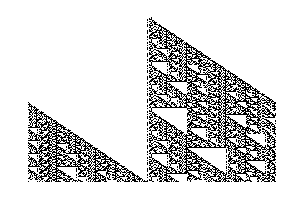
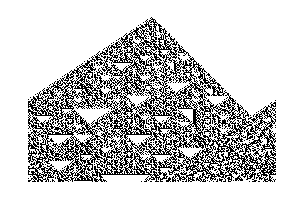

```mathematica
ArrayPlot[Identity[gateAutomaton[{True,True,False,False,True,False,True,False,False,False},#,200]]/.{True->1,False->0},ImageSize->Medium,PixelConstrained->True]&/@{{{{0,-2},Xor},{{-2,2},Xor},{{-1,2},Xor}},{{{2,1},Xor},{{0,-2},Xor},{{-2,1},Xor}}}
```

```mathematica
ArrayPlot[Identity[gateAutomaton[Join[Table[False,100],{True,False,True,False,True},Table[False,100]],#,200]]/.{True->1,False->0},PixelConstrained->True]&[{{{1},Not},{{1},Not},{{1},Not},{{1},Not},{{1,-1},Xor}}]
```

-Graphics-

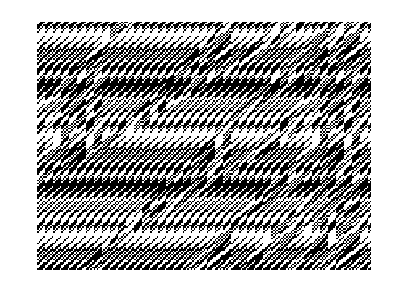

```mathematica
ArrayPlot[alternateArray[gateAutomaton[init,#,300]]/.{True->1,False->0},PixelConstrained->True]&[{{{1},Not},{{1},Not},{{1},Not},{{1},Not},{{1,-1},Xor}}]
```

```mathematica
ArrayPlot[alternateArray[gateAutomaton[init,#,100]]/.{True->1,False->0},PixelConstrained->True]&[randomRules[[10]]]
```

-Graphics-

```mathematica
#->ArrayPlot[alternateArray[gateAutomaton[init,#,100]]/.{True->1,False->0},PixelConstrained->True]&[{{-1,0,SameQ}}]
```

{{-1,0,SameQ}}→-Graphics-

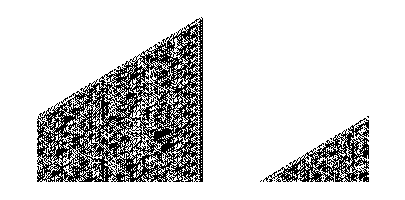
{{{1,2,-1},Xor},{{-2,-1},Or},{{1,-2,0},Xor},{{2,-2,-2},Xor},{{3,-1},Or}}→-Graphics-

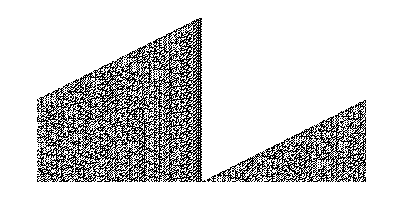
{{{-1,2},Xor},{{1,2},Xor},{{1,2},Or}}→-Graphics-

```mathematica
{{-1,0},Xor},{{-1,1},Xor},{{-1,1},Xor}
```

```mathematica
ArrayPlot[automaton/.{True->1,False->0},PixelConstrained->True,ImageSize->Large]
```

-Graphics-

```mathematica
#->ArrayPlot[gateAutomaton[init,#,600]/.{True->1,False->0},PixelConstrained->True,ImageSize->1000]&/@{{{{-1,0},Nor},{{-1,2},Xor}},{{{-1,0},Nor},{{1,2},Xor}},{{{-1,0},Nand},{{1,2},Xor}},{{{-1,1},Nor},{{1,2},Xor}},{{{-1,1},Or},{{1,2},Xor}},{{{-1,1},Nand},{{1,2},Xor}},{{{-1,1},Implies},{{1,2},Xor}},{{{-1,1},Or},{{-1,2},Xor}},{{{-1,1},Nand},{{-1,2},Xor}},{{{-1,1},Implies},{{-1,2},Xor}},{{{-1,2},Xor},{{0,1},Implies}}}
```

{{{{-1,0},Nor},{{-1,2},Xor}}→-Graphics-,{{{-1,0},Nor},{{1,2},Xor}}→-Graphics-,{{{-1,0},Nand},{{1,2},Xor}}→-Graphics-,{{{-1,1},Nor},{{1,2},Xor}}→-Graphics-,{{{-1,1},Or},{{1,2},Xor}}→-Graphics-,{{{-1,1},Nand},{{1,2},Xor}}→-Graphics-,{{{-1,1},Implies},{{1,2},Xor}}→-Graphics-,{{{-1,1},Or},{{-1,2},Xor}}→-Graphics-,{{{-1,1},Nand},{{-1,2},Xor}}→-Graphics-,{{{-1,1},Implies},{{-1,2},Xor}}→-Graphics-,{{{-1,2},Xor},{{0,1},Implies}}→-Graphics-}

```mathematica
#->ArrayPlot[gateAutomaton[init,#,800]/.{True->1,False->0},PixelConstrained->True,ImageSize->1000]&[{{{-1,1},Nor},{{1,2},Xor}}]
```

{{{-1,1},Nor},{{1,2},Xor}}→-Graphics-

```mathematica
plots=#->ArrayPlot[gateAutomaton[init,#,100]/.{True->1,False->0},PixelConstrained->True,ImageSize->Small]&/@{{{{-1,0},Nor},{{-1,2},Xor}},{{{-1,0},Nor},{{1,2},Xor}},{{{-1,1},Xor},{{-1,2},Nor}},{{{-1,1},Nor},{{-1,2},Xor}},{{{-1,1},Nor},{{1,2},Xor}},{{{-1,2},Xor},{{-1,0},Nor}},{{{-1,1},Or},{{-1,2},Xor}},{{{-1,1},Or},{{1,2},Xor}},{{{-1,0},Nand},{{1,2},Xor}},{{{-1,1},Nand},{{-1,2},Xor}},{{{-1,1},Nand},{{1,2},Xor}},{{{-1,1},Implies},{{-1,2},Xor}},{{{-1,1},Implies},{{1,2},Xor}},{{{-1,2},Xor},{{0,1},Implies}}}
```

{{{{-1,0},Nor},{{-1,2},Xor}}→-Graphics-,{{{-1,0},Nor},{{1,2},Xor}}→-Graphics-,{{{-1,1},Xor},{{-1,2},Nor}}→-Graphics-,{{{-1,1},Nor},{{-1,2},Xor}}→-Graphics-,{{{-1,1},Nor},{{1,2},Xor}}→-Graphics-,{{{-1,2},Xor},{{-1,0},Nor}}→-Graphics-,{{{-1,1},Or},{{-1,2},Xor}}→-Graphics-,{{{-1,1},Or},{{1,2},Xor}}→-Graphics-,{{{-1,0},Nand},{{1,2},Xor}}→-Graphics-,{{{-1,1},Nand},{{-1,2},Xor}}→-Graphics-,{{{-1,1},Nand},{{1,2},Xor}}→-Graphics-,{{{-1,1},Implies},{{-1,2},Xor}}→-Graphics-,{{{-1,1},Implies},{{1,2},Xor}}→-Graphics-,{{{-1,2},Xor},{{0,1},Implies}}→-Graphics-}

```mathematica
ArrayPlot[gateAutomaton[init,#,40]/.{True->1,False->0},ImageSize->Small,PixelConstrained->True]&/@randomRules
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}